# Vector Plots and Optimization

## Derek Prince Week 7 APPM 2450 - 003, Fall 2015 Due 9th October, 2015

```mathematica
Clear["Global`*"];
```

## Patrol Cabin Locations

```mathematica
f[x_,y_] = y(x^2-4)+(y^2-1);
```

“The main requirement is that the ground be level where the cabins are to be located.”

#### 1)

```mathematica
gradf[x_,y_] = D[f[x,y],{{x,y}}]
```

{2 x y,-4+x^2+2 y}

#### 2)

Gradien vector field alond with level curves of the surface

```mathematica
vecplot = VectorPlot[gradf[x,y], {x,-7,7},{y,-7,7}, FrameLabel->{"x","y"}];
contplot = ContourPlot[f[x,y], {x,-7,7},{y,-7,7},Contours->10, AxesLabel->{"x","y"}, ImageSize->Large];
```

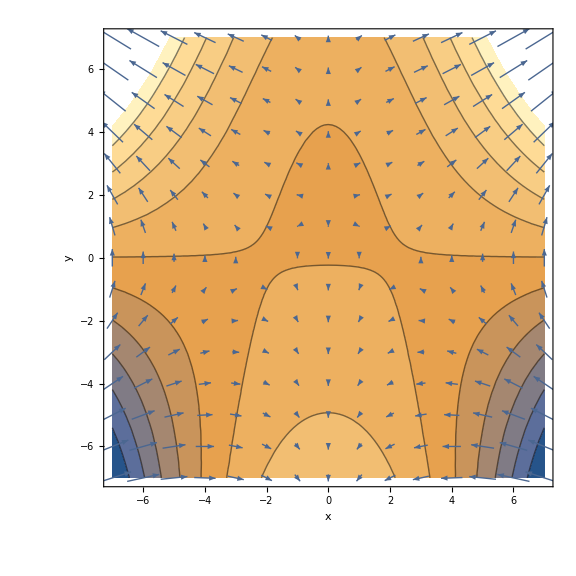

```mathematica
Show[contplot,vecplot]
```

```mathematica
surf = Plot3D[f[x,y], {x,-50,50},{y,-50,50}, ImageSize->Full];
```

#### 3)

Based on this plot, I expect the critical points to be (-2,0), (2,0), and (0,2) because there is a zero vector at each of those points.

#### 4)

```mathematica
cpts = Solve[gradf[x,y] ==0, {x,y}]
```

{{x→-2,y→0},{x→0,y→2},{x→2,y→0}}

Checking the values...

```mathematica
D[f[x,y],x]/.cpts[[1]]; (* Surpressed for clinliness -> they are all true 0's *)
D[f[x,y],x]/.cpts[[2]];
D[f[x,y],x]/.cpts[[3]];
D[f[x,y],y]/.cpts[[1]];
D[f[x,y],y]/.cpts[[2]];
D[f[x,y],y]/.cpts[[3]];
```

Make the graphics from the list of answers.

```mathematica
disk1 = Graphics[Disk[{x,y},0.25]]/.cpts[[1]];
disk2 = Graphics[Disk[{x,y},0.25]]/.cpts[[2]];
disk3 = Graphics[Disk[{x,y},0.25]]/.cpts[[3]];
```

#### 5)

Well, the assignment specifies a circular road so all the work is already done. Since it says nothing about it being a half circle, I will leave it as a full circle.
As the 0 vectors are all 2 units away from the origin, it’s simply a circle of radius 2, centered at the origin.

```mathematica
r[t_]= {2Cos[t],2Sin[t]};
road = ParametricPlot[r[t],{t,0,2π}];
```

#### 6)

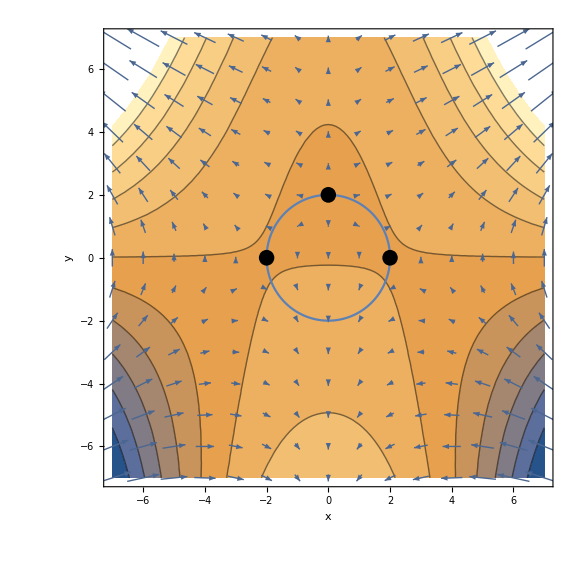

```mathematica
Show[contplot,vecplot,road, disk1,disk2,disk3]
```

It would have been easier and smoother to just make an inverted T-shaped road since that would follow the saddle of the land - but I guess they were tired of hearing “good enough for government work.”
More to the point, the road will be steepest at the bottom left and right, which is well documented by the fact that it lives beyond a higher contour plot line.

#### 7)

(a)
To get the slope of the

```mathematica
r[t]
```

{2 Cos[t],2 Sin[t]}